# Projekt 2: Integral

KTH/ICT:IX1304 - Matematik, Analys
Göran Andersson 2012/2013
Anna Delin 2013/2014
Senaste uppdatering 21 sept 2014.

## 1. Genomförande och bedömning

I den här projektuppgiften ingår att lösa två matematisk uppgifter, skriva en rapport i Mathematica och genomföra en kort muntlig presentation. Arbeta i grupp tillsammans med en annan student. Projektet berör centrala delar av kursinnehållet.

Viktigt: se till att din Mathematicakod hänger ihop med hjälp av (bland annat) ReplaceAll ( /. ) och Blank ( _ ). Det duger alltså inte att klistra in lösningar för hand i nästa kommando. Du kommer att bli ombedd att göra någon mindre ändring av problemformuleringen under redovisningen, och sedan köra om koden för det nya problemet. Försäkra dig därför själv om att din kod klarar av detta. Observera att du i dina lösningar skall visa att du behärskar de begrepp som analyskursen omfattar. Du får inte godkänt för “innovativa” lösningar som försöker kringgå begreppen i analyskursen (prövningar etc.). Alla axlar måste ha korrekta storheter utskrivna.

## 2. Förberedelser

### 2.1 Studier

Projektet handlar om integration. Lämpliga avsnitt i kursboken (Adams) är kapitel 5, 6 och 7. Sök gärna på nätet också på relevanta nyckelbegrepp.

### 2.2 Integralberäkning i Mathematica

Förutom genomgången nedan, läs om Integrateoch Limit i Documentation Center.

#### 2.2.1 Primitiv funktion

En obestämd integral eller primitiv funktion beräknas enligt syntaxen

Integrate[f[x], x]

Här följer ett par exempel:

```mathematica
ClearAll["`*"]
```

```mathematica
Integrate[x^2,x]
```

x^3/3

Funktionen som returneras är en generell primitiv funktion, som kan vara diskontinuerlig i vissa punkter.

```mathematica
f[x_]:=Log[1+x^2];
F[x_]=Integrate[Log[1+√(x^2)],x]
```

(-x^2+(x^2+√(x^2)) Log[1+√(x^2)])/x

```mathematica
F[0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

Antaganden kan ges via optionen Assumptions.

```mathematica
Integrate[Abs[x],x,Assumptions->x∈Reals]
```

Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]

Man kan även integrera symboliska uttryck:

```mathematica
Clear[f];
Integrate[f''[x]+2 a f'[x],x]
```

2 a f[x]+f'[x]

De uttryck som levereras är ofta funktioner av icke-elementär typ:

```mathematica
Integrate[Log[1+x]/x,x]
```

-PolyLog[2,-x]

Du får information om funktionen genom att markera funktionsnamnet den och trycka F1.

#### 2.2.2 Bestämd integral

En bestämd integral beräknas enligt syntaxen

Integrate[f[x], {x,a,b}]

Här följer ett par exempel:

```mathematica
ClearAll["`*"]
```

```mathematica
Integrate[x^2,{x,1,2}]
```

7/3

Antaganden kan ges via optionen Assumptions.

```mathematica
Integrate[x^a,{x,0,1},Assumptions-> a>-1]
```

1/(1+a)

Även generaliserade integraler kan beräknas:

```mathematica
∫_0^∞ ⅇ^(-x^2)ⅆx
```

(√π)/2

```mathematica
Limit[∫_0^b ⅇ^(-x^2)ⅆx,b->∞]
```

(√π)/2

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2)ⅆx
```

√π

```mathematica
Limit[Limit[∫_-a^b ⅇ^(-x^2)ⅆx,a->∞],b->∞]
```

√π

#### 2.2.3 Numerisk integration

Vid många tillfällen är det inte nödvändigt med symbolisk integration. Då är NIntegrate ett lämpligt alternativ:

NIntegrate[f[x], {x,a,b}]

Här följer ett par exempel:

```mathematica
ClearAll["`*"]
```

```mathematica
NIntegrate[E^(-t)Sin[10Pi t],{t,0,10}]
```

0.0317973

```mathematica
NIntegrate[√(1+Log[1+x]),{x,0,ⅇ}]
```

3.62318

#### 2.2.4 Flerdimensionell integration (för den intresserade)

Integraler kan även definieras i flera dimensioner. Integralen ∫_a^b f(x)dx ses ju som arean under f(x). I två dimensioner kan ∫_c^d ∫_a^b f(x,y)dx dy ses som volymen under ytan f(x,y).

```mathematica
ClearAll["`*"];
f[x_,y_]:=3-x^2/3-(2 y^2)/3;
Plot3D[f[x,y],{x,-2,2},{y,-1,1},PlotRange->{0,All},Filling->Axis,BoxRatios->Automatic,AxesLabel->{"x","y","f"}]
```

-Graphics3D-

Volymen på bilden kan beräknas med

```mathematica
Integrate[f[x, y], {x, -2, 2}, {y, -1, 1}]
```

56/3

Man kan även integrera över områden 𝒟 som inte är rektanglar. T.ex.

```mathematica
𝒟[x_,y_]:=(x-1)^2+(y-1/2)^2≤1;
```

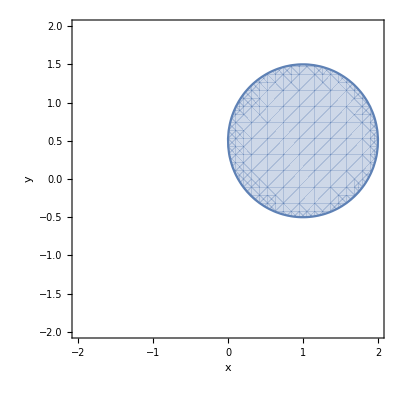

```mathematica
RegionPlot[𝒟[x,y],{x,-2,2},{y,-2,2},FrameLabel->{"x","y"}]
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2},PlotRange->{0,All},Filling->Axis,BoxRatios->Automatic,AxesLabel->{"x","y","f"},RegionFunction->Function[{x,y,z},𝒟[x,y]]]
```

-Graphics3D-

Volymen i detta fall blir:

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ f[x,y] Boole[𝒟[x,y]]ⅆyⅆx
```

(9 π)/4

För mer komplicerade integraler används i regel numerisk lösning med NIntegrate.

### 2.3 Differentialekvationer i Mathematica

Läs även om DSolve i Documentation Center.

Kommandot DSolve löser en differentialekvation enligt syntaxen

DSolve[eqn, y, x]

Exempel: 

Lös differentialekvationen y’(x) + y(x) = a sin(x). Konstanten a är godtycklig.

```mathematica
ClearAll["`*"]
DSolve[y'[x] + y[x] == a Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])}}

Lägg till randvillkoret y(0) = 0 :

```mathematica
ClearAll["`*"]
DSolve[{y'[x] + y[x] == a Sin[x], y[0] == 0},y[x],x]
```

{{y[x]→-1/2 a ⅇ^-x (-1+ⅇ^x Cos[x]-ⅇ^x Sin[x])}}

Lösningen ges av som vanligt av Mathematica som ett antal regler. För att kunna hantera lösningen med ytterligare kod, t ex för att plotta lösningen, använder vi ReplaceAll (/.):

```mathematica
ClearAll["`*"]
sol = DSolve[{y'[x] + y[x]== a Sin[x], y[0] == 0},y,x]
```

{{y→Function[{x},-1/2 a ⅇ^-x (-1+ⅇ^x Cos[x]-ⅇ^x Sin[x])]}}

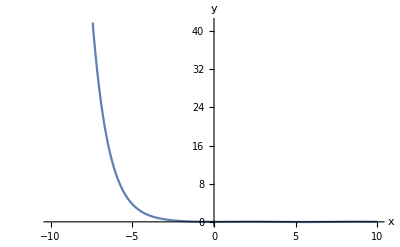

```mathematica
a = 0.05; (* vid plottning måste vi också anta ett värde på a *)
Plot[y[x]/.sol,{x,-10,10},AxesLabel->{x, y}]
```

## 3. Matematisk uppgift

### 3.1 Problem med integralkalkylens huvudsats

Du ska nu studera ett integralproblem med Mathematica. Definiera funktionen f(x)=√(p x^2+x^4),x∈ℝ, där p är din födelsedag (ett tal mellan 1 och 31). Läs igenom alla deluppgifter innan du börjar.

```mathematica
ClearAll["`*"]
```

Plotta f(x)  i lämpligt intervall.

```mathematica
p:= 20
```

```mathematica
f[x_]:=Sqrt[(p*x^2)+x^4]
```

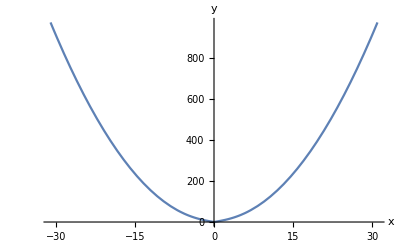

```mathematica
Plot[f[x],{x,-31,31},AxesLabel->{x,y}]
```

Bestäm med hjälp av Mathematica ∫_-1^2 f(x) dx, både numeriskt och exakt och jämför resultaten.

```mathematica
x1:=-1
```

```mathematica
x2:=2
```

```mathematica
Integrate[f[x],{x,x1,x2}]
```

-(80 √5)/3+16 √6+7 √21

```mathematica
NIntegrate[f[x],{x,x1,x2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

11.6414

Använd Mathematica för att bestämma en primitiv funktion F(x). Plotta F(x). Är den primitiva funktionen definierad överallt i intervallet [-1,2]? Beräkna höger och vänster gränsvärde för den problematiska punkten.

```mathematica
F[x_]=Integrate[f[x],x]
```

((x^2 (20+x^2))^(3/2))/(3 x^3)

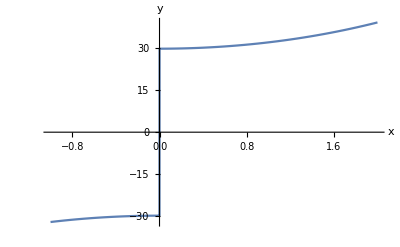

```mathematica
Plot[F[x],{x,x1,x2},AxesLabel->{x,y}]
```

```mathematica
Limit[F[x],x->0,Direction->-1]
```

(40 √5)/3

```mathematica
Limit[F[x],x->0,Direction->1]
```

-(40 √5)/3

Prova att beräkna integralen med huvudsatsen, dvs ∫_-1^2 f(x) dx=F(2)-F(-1). Försök förklara vad som är fel. Vilket är det korrekta värdet?

```mathematica
F[x2]-F[x1]
```

16 √6+7 √21

Skriv om ∫_-1^2 f(x) dx (t ex genom att dela upp integralen i två intervall) så att huvudsatsen kan användas.

```mathematica
NIntegrate[f[x],{x,0,2}]-Integrate[f[x],{x,0,-1}]
```

11.6414

Bestäm ∫_-1^2 f(x) dx för hand genom att använda substitionsmetoden. Integraltabeller ska alltså inte användas här.

### 3.2 En differentialekvation

Betrakta begynnelsevärdesproblemet

c'(t) = t^2 c^3 med begynnelsevillkor c(1) = p, där p är din födelsedag (ett tal mellan 1 och 31).

Lös problemet med hjälp av Mathematica. Plotta lösningen i lämpligt intervall. Markera begynnelsevillkoret med en röd punkt i plotten. Diskutera kvalitativt för vilka t din lösning gäller.

```mathematica
ClearAll["`*"]
```

```mathematica
p :=20

sol=DSolve[{ c'[t]==t^2*c[t]^3,c[1]==p},c[t], t];
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

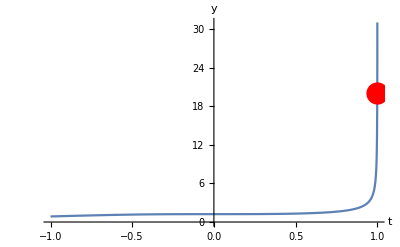

```mathematica
Plot[c[t]/.sol,{t,-1,2},AxesLabel->{t,y},PlotRange->{0,31},Epilog->{PointSize[.04], Red,Point[{1,p}]}]
```

```mathematica
Solve[Sqrt[803-800 t^3]==0]
```

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}

Lös problemet för hand (det är en separabel differentialekvation). Kontrollera att din lösning är rimlig genom att derivera den och visa att du får tillbaka den ursprungliga ekvationen. Kontrollera också att begynnelsevillkoret är uppfyllt. Jämför med din Mathematica-lösning.

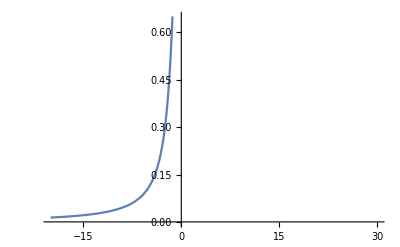

```mathematica
Plot[Sqrt[-0.5/((t^3)/3-0.5/20-1/3)],{t,-20,30}]
```

Differentialekvationen c’(t) = t^2 c^3(utan randvillkor) har två lösningsgrenar. Formulera ett nytt randvillkor så att den andra grenen utgör lösning. Plotta din lösning. Diskutera kvalitativt för vilka t din lösning gäller.

```mathematica
ClearAll["`*"]
```

```mathematica
sol=DSolve[ c'[t]==t^2*c[t]^3,c[t], t]
```

{{c[t]→-(√(3/2))/(√(-t^3-3 C[1]))},{c[t]→(√(3/2))/(√(-t^3-3 C[1]))}}

```mathematica
p:=-20;
```

```mathematica
sol=DSolve[{ c'[t]==t^2*c[t]^3,c[1]==p},c[t], t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{c[t]→-(20 √3)/(√(803-800 t^3))}}

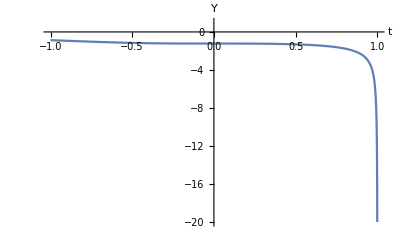

```mathematica
Plot[c[t]/.sol, {t, -1,2}, AxesLabel->{"t","Y"}, PlotRange->{p,1}]
```

```mathematica
Solve[-Sqrt[803-800 t^3]==0]
```

{{t→-(-803)^(1/3)/(2 10^(2/3))},{t→803^(1/3)/(2 10^(2/3))},{t→((-1)^(2/3) 803^(1/3))/(2 10^(2/3))}}